```mathematica
normalization[n_]:=2^n n!√π

H0[y_]:=a0
normH0=Integrate[Exp[-y^2] H0[y]^2,{y,-∞,∞}]
a0Sol=a0/.Solve[normH0==normalization[0]]
a0=Max[a0Sol]
H0[y]
```

a0^2 √π

{-1,1}

1

1

```mathematica
H1[y_]:=a1 y
normH1=Integrate[Exp[-y^2] H1[y]^2,{y,-∞,∞}]
a1Sol=a1/.Solve[normH1==normalization[1]]
a1=Max[a1Sol]
H1[y]
```

2 √π

{2}

2

2 y

```mathematica
a0=.
a2=-2a0
H2[y_]:=a0+a2 y^2
normH2=Integrate[Exp[-y^2] H2[y]^2,{y,-∞,∞}]
a2Sol=a0/.Solve[normH2==normalization[2]]
a0=Min[a2Sol]
H2[y]
```

-2 a0

2 a0^2 √π

{-2,2}

-2

-2+4 y^2

```mathematica
eqHermite[y_]:=2 n H[y]-2 y D [H[y],y]+H''[y]
```

```mathematica
eqHermite[y]/.n->0/.H-> H0//FullSimplify
```

0

```mathematica
eqHermite[y]/.n->1/.H-> H1//FullSimplify
```

0

```mathematica
eqHermite[y]/.n->2/.H-> H2//FullSimplify
```

0

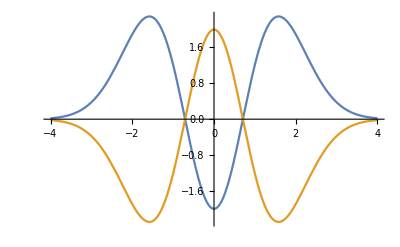

```mathematica
Plot[{Exp[-y^2/2]H2[y],-Exp[-y^2/2]H2[y]},{y,-4,4}]
```